```mathematica
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\Direct_Greens_Function\\rotsaw\\bin"];
```

```mathematica
t=1.0;
J=0.4t;
Emin=-6;
Emax=8;
Epoints=1401;
iδ=0.05I;
```

```mathematica
moves={"E","N","W","S"};
nodeUnits={1,I,-1,-I};
addMove[move_,path_:{}]:=Append[path,move];
getInvMove[move_]:=moves[[Mod[2+Position[moves,move][[1,1]],4,1]]];
refinePath[path_]:=(
refinedPath=path;
For[it=1,it<Length[refinedPath],it++,
If[refinedPath[[it]]==getInvMove[refinedPath[[it+1]]],
refinedPath[[it]]=Missing[];
refinedPath[[it+1]]=Missing[];
];
];
Return[DeleteMissing[refinedPath]]
);
nodeCast[path_]:=(
refinedPath=refinePath[path];
nodes={0};
Do[
AppendTo[nodes,nodes[[-1]]+nodeUnits[[Position[moves,move][[1,1]]]]],
{move,refinedPath}];
Return[nodes]
);
isSelfAvoiding[path_]:=(
nodes = nodeCast[path];
For[it=Length[nodes],it>1,it--,
For[jt=it-1,jt>0,jt--,If[nodes[[it]]==nodes[[jt]],Return[False]]];
];
Return[True];
);
getSelfAvoidingMoves[path_]:=(
Return[Pick[moves,Table[isSelfAvoiding[addMove[move,path]],{move,moves}]]];
);
```

```mathematica
getPhase[path_,m_]:=(
phase = 1;
For[i=1,i≤Length[path],i++,(
phase*=nodeUnits[[Position[moves,path[[i]]][[1,1]]]]^m[[i]];
)];
Return[phase];
);
getPaths[order_]:=(
paths={{}};
For[i=1,i≤order,i++,(
oldPaths=paths;
paths={};
Do[
Do[(
AppendTo[paths,addMove[move,path]]
),{move,moves}],
{path,oldPaths}];
)];
Return[paths];
);
getGFList[order_]:=(
paths=getPaths[order];
Return[Table[{lPath,rPath},{lPath,paths},{rPath,paths}]];
);
getGFPhases[order_,m_]:=(
paths=getPaths[order];
rPhases=Table[getPhase[path,m],{path,paths}];
lPhases=Conjugate[rPhases];
Return[Table[lPhase * rPhase,{lPhase,lPhases},{rPhase,rPhases}]];
);
refineGFPhases[GFList_,GFPhases_]:=(
refinedGFPhases={};
For[i=1,i≤Length[GFList],i++,(
For[j=1,j≤Length[GFList[[i]]],j++,(
GF=GFList[[i,j]];
If[isSelfAvoiding[GF[[1]]]&&isSelfAvoiding[GF[[2]]],(
AppendTo[refinedGFPhases,GFPhases[[i,j]]];
)];
)];
)];
Return[refinedGFPhases];
);
refineGFList[GFList_]:=(
refinedGFList={};
For[i=1,i≤Length[GFList],i++,(
For[j=1,j≤Length[GFList[[i]]],j++,(
GF=GFList[[i,j]];
If[isSelfAvoiding[GF[[1]]]&&isSelfAvoiding[GF[[2]]],(
AppendTo[refinedGFList,{refinePath[GF[[1]]], refinePath[GF[[2]]]}];
)];
)];
)];
Return[refinedGFList];
);
```

```mathematica
getGFPattern[GF_]:=(
singleLine=1;
doubleLine={};
denominator={{{},moves}};
lMax=Length[GF[[1]]];
rMax=Length[GF[[2]]];
tMin = Min[lMax,rMax];
For[it=1,it≤tMin,it++,(
lMove=GF[[1,it]];
rMove=GF[[2,it]];
If[lMove== rMove,(
AppendTo[doubleLine,{denominator[[-1,1]],DeleteCases[denominator[[-1,2]],lMove]}];
),(
singleLine*=t^2;
AppendTo[denominator,{GF[[2,1;;it]],DeleteCases[moves,getInvMove[rMove]]}];
)];
AppendTo[denominator,{GF[[1,1;;it]],DeleteCases[moves,getInvMove[lMove]]}];
)];
id=1;
tMax=Max[lMax,rMax];
If[lMax<rMax,id=2];
For[it=tMin+1,it≤tMax,it++,(
tMove=GF[[id,it]];
singleLine*=-t;
AppendTo[denominator,{GF[[id,1;;it]],DeleteCases[moves,getInvMove[tMove]]}];
)];
Return[<|single->singleLine,double->doubleLine,denom->denominator|>];
);

getGFPatternList[GFList_]:=(
Return[Table[getGFPattern[GF],{GF,GFList}]];
);

applySymmetry[SEList_]:=(
symSEList={};
For[it=1,it≤Length[SEList],it++,(
SE=SEList[[it]];
If[Length[SE]>0,(
move1=SE[[1]];
p0=Position[moves,move1][[1,1]]-1;
For[jt=1,jt≤Length[SE],jt++,(
SE[[jt]]=moves[[Mod[Position[moves,SE[[jt]]][[1,1]]-p0,4,1]]]
)];
doMirror=False;
For[jt=1,jt≤Length[SE],jt++,(
If[SE[[jt]]≠moves[[1]],(If[SE[[jt]]≠moves[[2]],doMirror=True];Break[])];
)];
If[doMirror,
For[kt=jt,kt≤Length[SE],kt++,(
If[SE[[kt]]==moves[[2]],SE[[kt]]=moves[[4]]];
If[SE[[kt]]==moves[[4]],SE[[kt]]=moves[[2]]];
)]
];
)];
AppendTo[symSEList,SE];
)];
Return[symSEList];
);

getSEList[GFPatternList_]:=(
Return[DeleteDuplicates[applySymmetry[DeleteDuplicates[Flatten[Table[(
localSEList={};
Do[Do[AppendTo[localSEList,Append[denominator[[1]],move]],{move,denominator[[2]]}],{denominator,GFPattern[denom]}];
localSEList),{GFPattern,GFPatternList}],1]]]]];
);
```

```mathematica
makeInputFile[SEList_,override_:False]:=Module[
{content,excludedFiles,fileName,excludedSE,localSEList=SEList},
content="";
If[Not[override],(
excludedFiles=FileNames["output\\SE_*"];
excludedSE={};
Do[(
fileName=FileNameTake[file];
excludedSE=StringSplit[StringTake[fileName,{4,Length[fileName]-5}],""];
localSEList=DeleteCases[localSEList,excludedSE];
),{file,excludedFiles}];
)];
Do[content=StringJoin[content,StringJoin[SE],"\n"],{SE,localSEList}];
Export["input.txt",content];
];

readSEFiles[SEList_]:=Module[
{output},
output=<||>;
Do[(
AssociateTo[output,SE->Flatten[Import[StringJoin["output\\SE_",StringJoin[SE],".txt"],"Table"]]];
),{SE,SEList}];
Return[output];
];
```

```mathematica
getSEForm[GFPattern_]:=Module[{SEForm,localSEForm},
<|
single->GFPattern[single],
double-> (
SEForm={};
Do[(
localSEForm={};
Do[AppendTo[localSEForm,Append[dLine[[1]],move]],{move,dLine[[2]]}];
AppendTo[SEForm,applySymmetry[localSEForm]];
),{dLine,GFPattern[double]}];
SEForm),
denom->(
SEForm={};
Do[(
localSEForm={};
Do[AppendTo[localSEForm,Append[denominator[[1]],move]],{move,denominator[[2]]}];
AppendTo[SEForm,applySymmetry[localSEForm]];
),{denominator,GFPattern[denom]}];
SEForm)
|>
];

getEnergy[path_]:=Module[
{energy=2J,it,nodes=nodeCast[path]},
For[it=1,it<Length[nodes],it++,(
energy+=2J;
Do[If[MemberQ[nodes,nodes[[it]]+move],energy-=J/2],{move,nodeUnits}]
)];
Return[energy];
];

getSymmetryFactor[SEPath_]:=Module[
{factor=1,is4Fold=True,isMirror=False},
is4Fold=SEPath=={"E"};
If[is4Fold,factor=4,(
isMirror=AllTrue[SEPath[[1;;-2]],#=="E"&]&&(SEPath[[-1]]≠"E");
If[isMirror,factor=2];
)];
Return[factor];
]

calculateGamma[SEPaths_]:=Module[
{path,energy,SEData,gamma,it,ωPoints,SEValue},
path=SEPaths[[1]][[1;;-2]];
energy=getEnergy[path];
ωPoints=Table[(Emax-Emin)*(it-1)/(Epoints-1)+Emin,{it,Epoints}];
gamma=Table[ωPoints[[it]]+iδ-energy,{it,Epoints}];
Do[(
SEData=SEDataSet[SEpath];
For[it=1,it≤Epoints,it++,(
SEValue=ToExpression[StringJoin["{",StringTake[SEData[[it]],{2;;-2}],"}"]];
gamma[[it]]-=(SEValue[[1]]+I SEValue[[2]])/getSymmetryFactor[SEpath];
)];
),{SEpath,SEPaths}];
Return[gamma];
];

makeGammaSet[GFPatternList_]:=Module[
{SEForm,localSEList,SEPaths,it,gammaSet=<||>},
Do[(
SEForm=getSEForm[GFPattern];
Do[(
localSEList=SEForm[spec];
For[it=1,it≤Length[localSEList],it++,(
SEPaths=localSEList[[it]];
If[Not[KeyExistsQ[gammaSet,GFPattern[spec][[it]]]],(
AssociateTo[gammaSet,GFPattern[spec][[it]]->calculateGamma[SEPaths]]
)]
)];
),{spec,{double,denom}}];
),{GFPattern,GFPatternList}];
Return[gammaSet];
];
```

```mathematica
calculateGFCoeff[GFPattern_]:=Module[
{numerator=1,denominator=1,dLine,it},
ndLines=Length[GFPattern[double]];
If[ndLines>0,(
dLine = gammaSet[GFPattern[double][[ndLines]]];
numerator*=dLine;
For[it=ndLines-1,it>0,it--,(
dLine=gammaSet[GFPattern[double][[it]]];
numerator=dLine-(t^2/numerator);
)];
)];
numerator*=GFPattern[single];
Do[denominator*=gammaSet[node],{node,GFPattern[denom]}];
Return[numerator/denominator];
];

getGFCoeffList[GFPatternList_]:=Module[
{GFCoeffList={}},
For[it=1,it≤Length[GFPatternList],it++,(
AppendTo[GFCoeffList,calculateGFCoeff[GFPatternList[[it]]]]
)];
Return[GFCoeffList];
];

calculateRotGF[order_,GFList_]:=Module[
{RotGF,RotCoeff,refPh,mList,tempList,mCases,it,jt,ωPoints},
RotGF=<||>;
mList={{}};
mCases={0,1,2,3};
For[it=1,it≤order,it++,(
tempList={};
Do[For[jt=1,jt≤Length[mList],jt++,(
AppendTo[tempList,Append[mList[[jt]],m]];
)],{m,mCases}];
mList=tempList;
)];
ωPoints=Table[(Emax-Emin)*(jt-1)/(Epoints-1)+Emin,{jt,Epoints}];
Do[(
refPh=refineGFPhases[GFList,getGFPhases[order,m]];
RotCoeff=Total[refPh*GFCoeffList]/Sqrt[Length[refPh]];
AssociateTo[RotGF,m->Table[{ωPoints[[it]],RotCoeff[[it]]},{it,Epoints}]];
),{m,mList}];
Return[RotGF];
];

getRotSF[RotGF_]:=Module[
{it,jt,RotSF,localRotGF,ωPoints},
Return[Association[Table[(localRotGF=Normal[RotGF][[it]];
localRotGF[[1]]-> Table[{localRotGF[[2,jt,1]],-Im[localRotGF[[2,jt,2]]]/Pi},
{jt,Length[localRotGF[[2]]]}]),
{it,Length[RotGF]}]]];
];
```

```mathematica
order=2;
GFList=getGFList[order];
refGFList=refineGFList[GFList];
GFPatternList=getGFPatternList[refGFList];
SEList=getSEList[getGFPatternList[refGFList]]
makeInputFile[SEList,True]
```

{{E},{E,E},{E,N},{E,E,E},{E,E,N},{E,N,E},{E,N,N},{E,N,W}}

```mathematica
(*RunProcess[{"/main.exe","14"},"ExitCode"]*)
SEDataSet=readSEFiles[SEList];
```

```mathematica
gammaSet=makeGammaSet[GFPatternList];
GFCoeffList=getGFCoeffList[GFPatternList];
RotGF=calculateRotGF[order,GFList];
rotSF=getRotSF[RotGF];
```

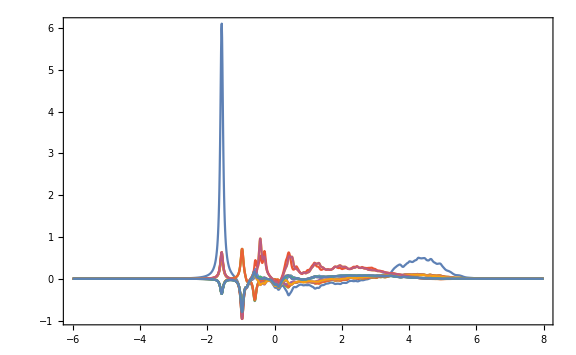

```mathematica
ListLinePlot[Table[rotSF[key],{key,Keys[rotSF]}],PlotRange->{{Emin,Emax},Full},Frame->True,Axes->{True,False},ImageSize->Large,FrameStyle->Directive[Black, 16]]
```

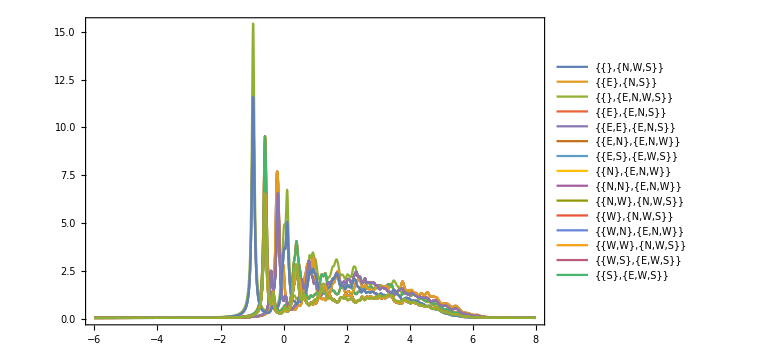

```mathematica
ListLinePlot[Im[gammaSet],PlotRange->{{Emin,Emax},Full},DataRange->{Emin,Emax},Frame->True,Axes->{True,False},ImageSize->Large,FrameStyle->Directive[Black, 16]]
```

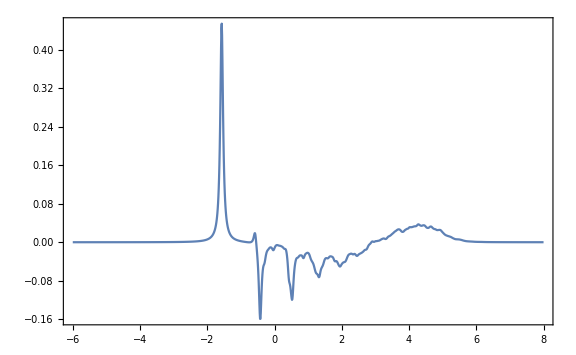

```mathematica
g1=gammaSet[{{},{"E","N","W","S"}}];
g2=gammaSet[{{"E"},{"E","N","S"}}];
g3=gammaSet[{{"E","E"},{"E","N","S"}}];
ListLinePlot[-Im[1/(g1 g2 g3)]/Pi,PlotRange->{{Emin,Emax},Full},DataRange->{Emin,Emax},Frame->True,Axes->{True,False},ImageSize->Large,FrameStyle->Directive[Black, 16]]
```

```mathematica
g1=gammaSet[{{},{"E","N","W","S"}}];
g2=gammaSet[{{"E"},{"E","N","S"}}];
g3=gammaSet[{{"E","E"},{"E","N","S"}}];
ListLinePlot[-Im[1/(g1 g2 g3)]/Pi,PlotRange->{{Emin,Emax},Full},DataRange->{Emin,Emax},Frame->True,Axes->{True,False},ImageSize->Large,FrameStyle->Directive[Black, 16]]
```

-Graphics-

```mathematica
pos=Position[Flatten[GFList,1],{{"E","E"},{"E","W"}}][[1,1]]
refGFList[[pos]]
GFPatternList[[pos]]
```

3

{{E,E},{}}

<|single→1.,double→{},denom→{{{},{E,N,W,S}},{{E},{E,N,S}},{{E,E},{E,N,S}}}|>